```mathematica
Clear["Global`*"]
<< FeynArts`
<< FeynArts`Insert`
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

Global`Insert`

```mathematica
top=CreateTopologies[0,2->4];
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][7]],Propagator[Incoming][Vertex[1][2],Vertex[4][7]],Propagator[Outgoing][Vertex[1][3],Vertex[3][8]],Propagator[Outgoing][Vertex[1][4],Vertex[3][9]],Propagator[Outgoing][Vertex[1][5],Vertex[3][8]],Propagator[Outgoing][Vertex[1][6],Vertex[3][9]],Propagator[Internal][Vertex[3][8],Vertex[4][7]],Propagator[Internal][Vertex[3][9],Vertex[4][7]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],Propagator[Incoming][Vertex[1][2],Vertex[3][7]],Propagator[Outgoing][Vertex[1][3],Vertex[3][8]],Propagator[Outgoing][Vertex[1][4],Vertex[3][9]],Propagator[Outgoing][Vertex[1][5],Vertex[3][8]],Propagator[Outgoing][Vertex[1][6],Vertex[3][9]],Propagator[Internal][Vertex[3][7],Vertex[3][10]],Propagator[Internal][Vertex[3][8],Vertex[3][10]],Propagator[Internal][Vertex[3][9],Vertex[3][10]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],Propagator[Incoming][Vertex[1][2],Vertex[3][8]],Propagator[Outgoing][Vertex[1][3],Vertex[3][9]],Propagator[Outgoing][Vertex[1][4],Vertex[3][10]],Propagator[Outgoing][Vertex[1][5],Vertex[3][9]],Propagator[Outgoing][Vertex[1][6],Vertex[3][10]],Propagator[Internal][Vertex[3][7],Vertex[3][8]],Propagator[Internal][Vertex[3][7],Vertex[3][9]],Propagator[Internal][Vertex[3][8],Vertex[3][10]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],Propagator[Incoming][Vertex[1][2],Vertex[3][8]],Propagator[Outgoing][Vertex[1][3],Vertex[3][9]],Propagator[Outgoing][Vertex[1][4],Vertex[3][10]],Propagator[Outgoing][Vertex[1][5],Vertex[3][9]],Propagator[Outgoing][Vertex[1][6],Vertex[3][10]],Propagator[Internal][Vertex[3][7],Vertex[3][8]],Propagator[Internal][Vertex[3][7],Vertex[3][10]],Propagator[Internal][Vertex[3][8],Vertex[3][9]]]]

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

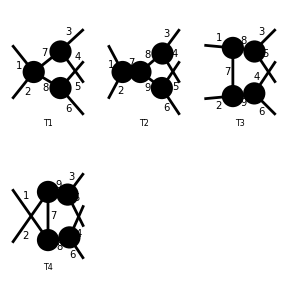

```mathematica
top3546=TopologyList[Level[top,1][[104]],Level[top,1][[119]],Level[top,1][[213]],Level[top,1][[214]]]
Paint[top3546,FieldNumbers->True];
```

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

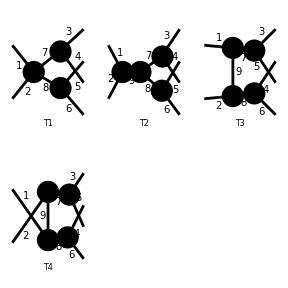

```mathematica
(*Modify the topology list by hand in a way that equivalent lines have the same FieldNumber. This is necessary to assign the diagrams to the correct resonant channel structure in InsertFields(which is difficult if the fields that couple to the same final state particles have different indices)*)
top3546 = TopologyList[
	Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][7]],
	Propagator[Incoming][Vertex[1][2],Vertex[4][7]],
	Propagator[Outgoing][Vertex[1][3],Vertex[3][8]],
	Propagator[Outgoing][Vertex[1][4],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][5],Vertex[3][8]],
	Propagator[Outgoing][Vertex[1][6],Vertex[3][9]],
	Propagator[Internal][Vertex[3][8],Vertex[4][7]],
	Propagator[Internal][Vertex[3][9],Vertex[4][7]]],
	Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],
	Propagator[Incoming][Vertex[1][2],Vertex[3][7]],
	Propagator[Outgoing][Vertex[1][3],Vertex[3][8]],
	Propagator[Outgoing][Vertex[1][4],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][5],Vertex[3][8]],
	Propagator[Outgoing][Vertex[1][6],Vertex[3][9]],
	Propagator[Internal][Vertex[3][8],Vertex[3][10]],
	Propagator[Internal][Vertex[3][9],Vertex[3][10]],Propagator[Internal][Vertex[3][7],Vertex[3][10]]],
	Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],
	Propagator[Incoming][Vertex[1][2],Vertex[3][8]],
	Propagator[Outgoing][Vertex[1][3],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][4],Vertex[3][10]],
	Propagator[Outgoing][Vertex[1][5],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][6],Vertex[3][10]],
	Propagator[Internal][Vertex[3][7],Vertex[3][9]],
	Propagator[Internal][Vertex[3][8],Vertex[3][10]],
Propagator[Internal][Vertex[3][7],Vertex[3][8]]],
	Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],
	Propagator[Incoming][Vertex[1][2],Vertex[3][8]],
	Propagator[Outgoing][Vertex[1][3],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][4],Vertex[3][10]],
	Propagator[Outgoing][Vertex[1][5],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][6],Vertex[3][10]],
Propagator[Internal][Vertex[3][8],Vertex[3][9]],
	Propagator[Internal][Vertex[3][7],Vertex[3][10]],
Propagator[Internal][Vertex[3][7],Vertex[3][8]]]];
Paint[top3546,FieldNumbers->True];
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][7]],Propagator[Incoming][Vertex[1][2],Vertex[4][7]],Propagator[Outgoing][Vertex[1][3],Vertex[3][8]],Propagator[Outgoing][Vertex[1][4],Vertex[3][9]],Propagator[Outgoing][Vertex[1][5],Vertex[3][9]],Propagator[Outgoing][Vertex[1][6],Vertex[3][8]],Propagator[Internal][Vertex[3][8],Vertex[4][7]],Propagator[Internal][Vertex[3][9],Vertex[4][7]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],Propagator[Incoming][Vertex[1][2],Vertex[3][8]],Propagator[Outgoing][Vertex[1][3],Vertex[3][9]],Propagator[Outgoing][Vertex[1][4],Vertex[3][10]],Propagator[Outgoing][Vertex[1][5],Vertex[3][10]],Propagator[Outgoing][Vertex[1][6],Vertex[3][9]],Propagator[Internal][Vertex[3][7],Vertex[3][8]],Propagator[Internal][Vertex[3][7],Vertex[3][10]],Propagator[Internal][Vertex[3][8],Vertex[3][9]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],Propagator[Incoming][Vertex[1][2],Vertex[3][7]],Propagator[Outgoing][Vertex[1][3],Vertex[3][8]],Propagator[Outgoing][Vertex[1][4],Vertex[3][9]],Propagator[Outgoing][Vertex[1][5],Vertex[3][9]],Propagator[Outgoing][Vertex[1][6],Vertex[3][8]],Propagator[Internal][Vertex[3][7],Vertex[3][10]],Propagator[Internal][Vertex[3][8],Vertex[3][10]],Propagator[Internal][Vertex[3][9],Vertex[3][10]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],Propagator[Incoming][Vertex[1][2],Vertex[3][8]],Propagator[Outgoing][Vertex[1][3],Vertex[3][9]],Propagator[Outgoing][Vertex[1][4],Vertex[3][10]],Propagator[Outgoing][Vertex[1][5],Vertex[3][10]],Propagator[Outgoing][Vertex[1][6],Vertex[3][9]],Propagator[Internal][Vertex[3][7],Vertex[3][8]],Propagator[Internal][Vertex[3][7],Vertex[3][9]],Propagator[Internal][Vertex[3][8],Vertex[3][10]]]]

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

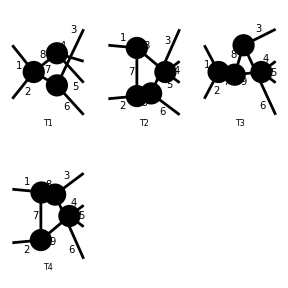

```mathematica
top3645=TopologyList[Level[top,1][[106]],Level[top,1][[220]],Level[top,1][[122]],Level[top,1][[219]]]
Paint[top3645,FieldNumbers->True];
```

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

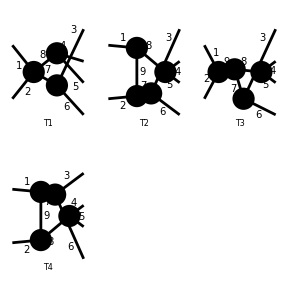

```mathematica
(*Modify the topology list by hand in a way that equivalent lines have the same FieldNumber. This is necessary to assign the diagrams to the correct resonant channel structure in InsertFields(which is difficult if the fields that couple to the same final state particles have different indices)*)
top3645 = TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][7]],Propagator[Incoming][Vertex[1][2],Vertex[4][7]],Propagator[Outgoing][Vertex[1][3],Vertex[3][8]],Propagator[Outgoing][Vertex[1][4],Vertex[3][9]],Propagator[Outgoing][Vertex[1][5],Vertex[3][9]],Propagator[Outgoing][Vertex[1][6],Vertex[3][8]],Propagator[Internal][Vertex[3][8],Vertex[4][7]],Propagator[Internal][Vertex[3][9],Vertex[4][7]]],
	Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],
	Propagator[Incoming][Vertex[1][2],Vertex[3][8]],
	Propagator[Outgoing][Vertex[1][3],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][4],Vertex[3][10]],
	Propagator[Outgoing][Vertex[1][5],Vertex[3][10]],
	Propagator[Outgoing][Vertex[1][6],Vertex[3][9]],
	Propagator[Internal][Vertex[3][8],Vertex[3][9]],
Propagator[Internal][Vertex[3][7],Vertex[3][10]],
Propagator[Internal][Vertex[3][7],Vertex[3][8]]],
	Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],
	Propagator[Incoming][Vertex[1][2],Vertex[3][7]],
	Propagator[Outgoing][Vertex[1][3],Vertex[3][8]],
	Propagator[Outgoing][Vertex[1][4],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][5],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][6],Vertex[3][8]],
	Propagator[Internal][Vertex[3][8],Vertex[3][10]],
	Propagator[Internal][Vertex[3][9],Vertex[3][10]],
Propagator[Internal][Vertex[3][7],Vertex[3][10]]],
	Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][7]],
	Propagator[Incoming][Vertex[1][2],Vertex[3][8]],
	Propagator[Outgoing][Vertex[1][3],Vertex[3][9]],
	Propagator[Outgoing][Vertex[1][4],Vertex[3][10]],
	Propagator[Outgoing][Vertex[1][5],Vertex[3][10]],
	Propagator[Outgoing][Vertex[1][6],Vertex[3][9]],
Propagator[Internal][Vertex[3][7],Vertex[3][9]],
Propagator[Internal][Vertex[3][8],Vertex[3][10]],
Propagator[Internal][Vertex[3][7],Vertex[3][8]]]];
Paint[top3645,FieldNumbers->True];
```